# Demonstration of using Vector Slicer Integration module

## Setup

### Configuration

Change these variables in order to change the slicing precision and size of the path so that it agrees with the experimental values. 
Note: All units in this notebook are specified in mm.

```mathematica
printWidthMillimetre= 0.2;
printWidthPixel= 9;
vectorSlicerDirectory=ParentDirectory[NotebookDirectory[],1];
```

### Automated setup

```mathematica
AppendTo[$Path,NotebookDirectory[]];
Needs["VectorSlicerIntegration`"]
```

```mathematica
patternExportDirectory=FileNameJoin[{vectorSlicerDirectory,"patterns"}];

fillMatrixDirectory=FileNameJoin[{vectorSlicerDirectory,"output","filled_matrices"}];
saveDirectory=FileNameJoin[{vectorSlicerDirectory,"output","optimisation_save"}];
lineSourceDirectory=FileNameJoin[{vectorSlicerDirectory,"output","paths"}];

outputDirectory=FileNameJoin[{NotebookDirectory[],"Images"}];
If[! TrueQ @ FileExistsQ  @ outputDirectory,CreateDirectory[outputDirectory]];
SetDirectory[outputDirectory];
```

Redefinition of functions to avoid repeating of all directory names

```mathematica
LocalGenerateInputFromCartesianTheta[patternName_,region_,θDirector_,fillingMethod_]:=GenerateInputFromCartesianTheta[patternExportDirectory,patternName,region,θDirector,printWidthMillimetre,printWidthPixel,fillingMethod]

LocalGenerateInputFromCartesianDirector[patternName_,region_,θDirector_,fillingMethod_]:=GenerateInputFromCartesianDirector[patternExportDirectory,patternName,region,θDirector,printWidthMillimetre,printWidthPixel,fillingMethod]

LocalGenerateInputFromRadialTheta[patternName_,region_,θDirector_,fillingMethod_]:=GenerateInputFromRadialTheta[patternExportDirectory,patternName,region,θDirector,printWidthMillimetre,printWidthPixel,fillingMethod]

LocalPlotFillMatrix[patternName_]:=PlotFillMatrix[fillMatrixDirectory,patternName]

LocalPlotPrintingMoves[patternName_]:=PlotPrintingMoves[lineSourceDirectory,patternName]

LocalPlotSlicedPattern[patternName_]:=PlotSlicedPattern[fillMatrixDirectory,lineSourceDirectory,patternName]

LocalExportSlicedPattern[patternName_]:=ExportSlicedPattern[fillMatrixDirectory,lineSourceDirectory,patternName]

LocalPlotOptimisationSequence[patternName_]:=PlotOptimisationSequence[saveDirectory,patternName]
```

## Generating input files

### Region definitions

```mathematica
disk[r_]:=Region[Disk[{0,0},r]]
annulus[rIn_,rOut_]:=Annulus[{0,0},{rIn,rOut}]
rectangle[a_,b_]:=Region[Rectangle[{-a/2,-b/2},{a/2,b/2}]]
cross[l_,w_]:=RegionUnion[rectangle[l,w],rectangle[w,l]]
```

### Director definitions

#### Cartesian director patterns

```mathematica
uniaxialLongitudinalDirector[{x_,y_}]=0;
uniaxialTransverseDirector[{x_,y_}]=π/2;
uniaxialDiagonalDirector[{x_,y_}]=π/4;

uniaxialLongitudinalCrossDirector[{x_,y_}]=Piecewise[{{0,Abs[x]>=Abs[y]}},π/2];
uniaxialTransverseCrossDirector[{x_,y_}]=Piecewise[{{π/2,Abs[x]>=Abs[y]}},0];
```

#### Radially symmetric director patterns

```mathematica
radialDirector[r_]=0;
azimuthalDirector[r_]=π/2;
```

### Exporting patterns

Filling methods can be “Splay”, “Perimeter” or “Dual”. See the manuscript for more details on the difference between them and guide as to when to use them.

#### Cartesian director patterns

```mathematica
LocalGenerateInputFromCartesianTheta["example_longitudinal_20_10_mm",rectangle[20,10],uniaxialLongitudinalDirector,"Perimeter"];
LocalGenerateInputFromCartesianTheta["example_diagonal_20_10_mm",rectangle[20,10],uniaxialDiagonalDirector,"Perimeter"];
```

```mathematica
LocalGenerateInputFromCartesianTheta["example_longitudinal_cross_20_5_mm",cross[20,5],uniaxialLongitudinalCrossDirector,"Perimeter"];
LocalGenerateInputFromCartesianTheta["example_transverse_cross_20_5_mm",cross[20,5],uniaxialTransverseCrossDirector,"Perimeter"];
```

#### Radially symmetric director patterns

```mathematica
LocalGenerateInputFromRadialTheta["example_radial_10_mm",disk[10],radialDirector,"Perimeter"];
LocalGenerateInputFromRadialTheta["example_azimuthal_10_mm",disk[10],azimuthalDirector,"Perimeter"];

LocalGenerateInputFromRadialTheta["example_azimuthal_10_mm_square",rectangle[20,20],azimuthalDirector,"Perimeter"];
```

## Reading results

## Results

### Demonstration of three methods of visualisation of slicing output

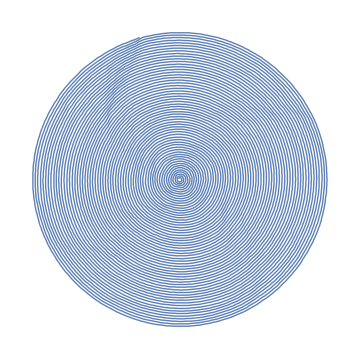
Fill matrix | Printer movements | Fill matrix + printer movements
-Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[{{"Fill matrix","Printer movements", "Fill matrix + printer movements"},
{LocalPlotFillMatrix["example_azimuthal_10_mm"],LocalPlotPrintingMoves["example_azimuthal_10_mm"],LocalPlotSlicedPattern["example_azimuthal_10_mm"]}}]
```

### Results of slicing example patterns

```mathematica
Row[{
LocalPlotSlicedPattern["example_longitudinal_20_10_mm"],
LocalPlotSlicedPattern["example_diagonal_20_10_mm"],
LocalPlotSlicedPattern["example_longitudinal_cross_20_5_mm"],
LocalPlotSlicedPattern["example_transverse_cross_20_5_mm"]}
]
```

-Graphics--Graphics--Graphics--Graphics-

```mathematica
Row[{
LocalPlotSlicedPattern["example_radial_10_mm"],
LocalPlotSlicedPattern["example_azimuthal_10_mm"],
LocalPlotSlicedPattern["example_azimuthal_10_mm_square"]}
]
```

-Graphics--Graphics--Graphics-

### Progress of penalty function decrease

For splay-free director patterns, the penalty function reaches lower values due to the existence of an ideal filling.

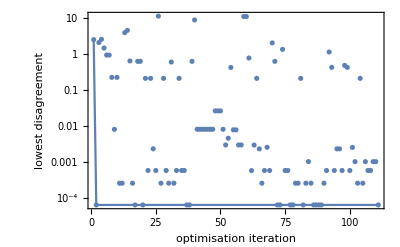

```mathematica
LocalPlotOptimisationSequence["example_longitudinal_20_10_mm"]
```

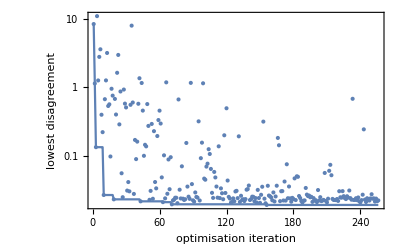

```mathematica
LocalPlotOptimisationSequence["example_azimuthal_10_mm"]
```

When patterns contain getSplay the penalty function does not decrease to similarly low values.

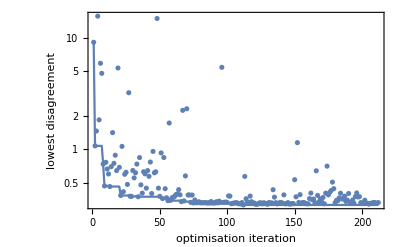

```mathematica
LocalPlotOptimisationSequence["example_radial_10_mm"]
```